# Lecture 30: Other Eigenvalue Algorithms Jacobi, Bisection, Divide and Conquer

There are other competitive direct eigen solvers.

## Oldest Eigenvalue Algorithm: Jacobi

Before the word “matrix” existed Jacobi needed to compute what would be called the eigenvalues of a real symmetric 7×7 matrix: there were only seven known planets at the time! He invented what is now called the Jacobi method!

#### Background and Code

We can diagonalize a symmetric 2 by 2 matrix using the Givens rotation (p1 | p2
-p2 | p1).   Lets work out the recipe!

```mathematica
AHat=({{p1, p2}, {-p2, p1}}).({{a11, a12}, {a12, a22}}).({{p1, -p2}, {p2, p1}});
MatrixForm[AHat]
```

(p1 (a11 p1+a12 p2)+p2 (a12 p1+a22 p2) | -p2 (a11 p1+a12 p2)+p1 (a12 p1+a22 p2)
p1 (a12 p1-a11 p2)+p2 (a22 p1-a12 p2) | -p2 (a12 p1-a11 p2)+p1 (a22 p1-a12 p2))

There are two values of p1 that work for any p2! Of course, we need to check that the expression under the square root is not negative if we want a real computation.

```mathematica
Solve[AHat⟦1,2⟧==0,p1]
```

{{p1→(a11 p2-a22 p2-√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)},{p1→(a11 p2-a22 p2+√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)}}

It is OK since a11^2+4 a12^2-2 a11 a22+a22^2=(a11-a22)^2+4 a12^2.  In practice, we should choose which solution we use carefully.  For now I am going to use the first one! Remember for the Givens matrices we need ||{p1,p2}||=1.

```mathematica
JMat[{{a11_,a12_},{a21_,a22_}}]:=Module[{p1,p2=1},
p1=(a11-a22-√((a11-a22)^2+4 a12^2))/(2 a12);
{p1,p2}=Normalize[{p1,p2}];
({{p1, p2}, {-p2, p1}})
]
```

As always test

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
G=JMat[A];
GAGt=G.A.Gᵀ;
Map[MatrixForm,{G.Gᵀ,GAGt}];
MatrixPlot[Chop[GAGt],PlotLegends->Automatic]
```

-Graphics-

To use this in a larger matrix we target a specific entry {i,j} and embed the appropriate tiny rotation in the identity matrix.

```mathematica
SetAttributes[BigJ,HoldFirst];
BigJ[A_,{i_,j_}]:=Module[{m=Length[A],G},
G=IdentityMatrix[m];
G⟦{i,j},{i,j}⟧=JMat[A⟦{i,j},{i,j}⟧];
G
]
```

As always test!

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
{i,j}={1,5};
G=BigJ[A,{i,j}];
GAGt=G.A.Gᵀ;
TabView[Map[MatrixPlot,Chop[{GAGt,G,G.Gᵀ,A}]]]
```

1234

So lets try to string a few of these together. It works just the way we expect if we are careful not to overlap!

```mathematica
m=7;
A=A0=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{3,4},{5,6}}}];
SetOptions[MatrixPlot, 
ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
```

123

If we overlap zeros that were made earlier get messed up.

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}}];
SetOptions[MatrixPlot, ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
MatrixForm[A]
```

{{-0.080919,0.583283,-0.683814,0.377432,-0.509303,-0.942687,1.08742},{0.583283,1.69082,0.753464,0.575205,1.42253,-0.510261,-0.938563},{-0.683814,0.753464,0.770462,0.049387,1.00186,0.892969,0.847836},{0.377432,0.575205,0.049387,1.65438,-0.870101,-1.68322,-0.447118},{-0.509303,1.42253,1.00186,-0.870101,0.983722,0.543581,0.138338},{-0.942687,-0.510261,0.892969,-1.68322,0.543581,0.862603,1.21398},{1.08742,-0.938563,0.847836,-0.447118,0.138338,1.21398,-0.687621}}

123456

(-2.3469 | 0.653997 | 0.0614361 | 0.137845 | 0.0374645 | 0.834888 | 1.19979×10^-17
0.653997 | 1.86561 | 0.456196 | 0.678132 | 1.18377 | 0.762214 | -0.183978
0.0614361 | 0.456196 | 1.26854 | -0.0544363 | 1.30494 | -1.14936 | 0.178252
0.137845 | 0.678132 | -0.0544363 | 1.67007 | -0.883674 | 1.69402 | -0.312744
0.0374645 | 1.18377 | 1.30494 | -0.883674 | 1.00856 | -0.548954 | -0.0322495
0.834888 | 0.762214 | -1.14936 | 1.69402 | -0.548954 | 0.862715 | -0.863129
2.22045×10^-16 | -0.183978 | 0.178252 | -0.312744 | -0.0322495 | -0.863129 | 0.864853)

Jacobi (or more likely one of his helpers aka computers or computes) was doing this by hand and would have been painstakingly updating a block of numbers.

You would like to be done as fast as possible.

You can do any of the entries.

Which one should you do?

Jacobi’s plan was “do the big ones first!”  This assumes that arithmetic is slow (it was then) and that it is fast (true for a small matrix) to find the biggest entry.

```mathematica
SetAttributes[JacobiStep, HoldFirst]
JacobiStep[A_]:= Module[{AbsA=Abs[UpperTriangularize[A,1]],ij,G},
(* Find the largest non-diagonal entry *)
ij=Position[AbsA,Max[AbsA]]⟦1⟧;
(* Compute the Jacobi/Given rotation zapping the biggest entry *)
G=BigJ[A,ij];
(* Update A in place *)
A=G.A.Gᵀ;
(* No need to return anything! *)
]
```

As always test.

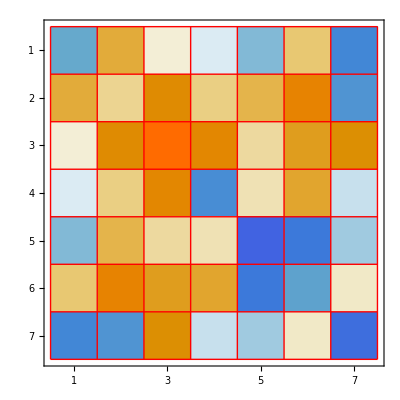
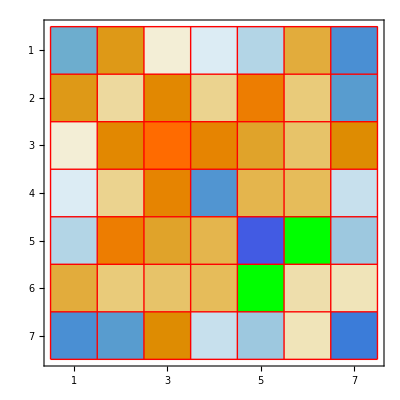

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
JacobiStep[A]
Map[MatrixPlot,Chop[{A0,A}]]
```

Now we can do a bunch and know that we are always targeting (and zeroing) large entries! This ensures it always makes progress and that it converges fast at the end!  Of course, copying and pasting is not a good plan! After a few steps the off-diagonal is looking fairly pale!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
TabView[{
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]]}]
```

12345678

Automation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=16;
TabView[Table[
JacobiStep[A];MatrixPlot[Chop[A]],
{MaxIter}]]
```

12345678910111213141516

#### Demo

Animation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=89;
ListAnimate[Table[
JacobiStep[A];MatrixPlot[Chop[A],PlotLabel->i],
{i,MaxIter}],8]
```

Things to note, something about our choices is pushing the negative eigenvalues up and the positive eigenvalues down!  Other choices will do other things! The common choice is to push the big (either positive or negative eigenvalues up) and the small eigenvalues down!

This algorithm has more parallelism the standard “QR” Francis algorithm we are going to learn.  It has a developed very quaternionic G4 version that block diagonalizes symmetric matrices.  I am working on an alternative G4 and a G8 algorithm that make progress with a simple plan of “move the big entries up”.

## Much Newer: Non Symmetric Jacobi

#### 2×2 Diagonalization

We can make a general 2 by 2 matrix upper triangular using the Givens rotation (p1 | p2
-p2 | p1).   Lets work out the recipe!

```mathematica
AHat=({{p1, p2}, {-p2, p1}}).({{a11, a12}, {a21, a22}}).({{p1, -p2}, {p2, p1}});
MatrixForm[AHat]
```

(p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2) | -p2 (a11 p1+a21 p2)+p1 (a12 p1+a22 p2)
p1 (a21 p1-a11 p2)+p2 (a22 p1-a12 p2) | -p2 (a21 p1-a11 p2)+p1 (a22 p1-a12 p2))

There are two values of p1 that work for any p2! Of course, we need to check that the expression under the square root is not negative if we want a real computation.

```mathematica
Solve[AHat⟦2,1⟧==0,p1]
```

{{p1→(a11 p2-a22 p2-√(a11^2+4 a12 a21-2 a11 a22+a22^2) p2)/(2 a21)},{p1→(a11 p2-a22 p2+√(a11^2+4 a12 a21-2 a11 a22+a22^2) p2)/(2 a21)}}

#### xxx

```mathematica
Simplify[AHat⟦1,1⟧]
Simplify[AHat⟦1,2⟧]
Hmm=D[AHat⟦1,1⟧+AHat⟦1,2⟧,{{p1,p2}}]
Hmm=Normal[CoefficientArrays[Hmm,{p1,p2}]⟦2⟧];
MatrixForm[Hmm]
```

a11 p1^2+p2 (a12 p1+a21 p1+a22 p2)

-p2 (a11 p1+a21 p2)+p1 (a12 p1+a22 p2)

{2 a11 p1+2 a12 p1-a11 p2+a12 p2+a21 p2+a22 p2,-a11 p1+a12 p1+a21 p1+a22 p1-2 a21 p2+2 a22 p2}

(2 a11+2 a12 | -a11+a12+a21+a22
-a11+a12+a21+a22 | -2 a21+2 a22)

```mathematica
{{Simplify[p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2), -p2 (a11 p1+a21 p2)+p1 (a12 p1+a22 p2)}}]
```

Syntax::bktmop: Expression "Simplify[p1(a11p1+a21p2)+p2(a12p1+a22p2) | -p2(a11p1+a21p2)+p1(a12p1+a22p2)]" has no opening "[".

#### xxx

It would be OK if a11^2+4 a12*a21-2 a11 a22+a22^2=(a11-a22)^2+4 a12*a21 is positive. Conditions like this are unavoidable.  Non-symmetric matrices can have complex eigenvalues which are non diagonalizable with real rotations!

An alternative would be to make the bottom entry as small as possible!  It turns out it is easier to make the 11 entry as large (in absolute value) as possible. We want to maximize 
	f[{p1,p2}]=p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2) 
subject to 
	g({p1,p2}]=p1^2+p2^2==1
This is just a standard Lagrange Multiplier problem.  If you go back and look in your calculus book you find that we want to find p satisfying||p||=1and 
	∇f(p)=λ ∇g(p)
Computing the derivatives is simple ∇g(p)=2p and ∇f(p)=B.p where 
	B=2(a_11 | 0.5(a_12+a_21)
0.5(a_12+a_21) | a_22) 
If we write p=v this looks familiar since we need to solve B.v=λ v  with ||v||=1.  It is a symmetric eigenvalue problem!  The eigenvector associated with the biggest eigenvalue gives the maximum and the smallest eigenvector gives the minimum.

```mathematica
MatrixForm[D[p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2),{{p1,p2}}]]
```

(2 a11 p1+a12 p2+a21 p2
a12 p1+a21 p1+2 a22 p2)

In practice, we should choose which solution we use carefully.  The  For now I am going to use the first one! Remember for the Givens matrices we need ||{p1,p2}||=1.

```mathematica
JMatNonSym[{{a11_,a12_},{a21_,a22_}}]:=Module[{a,p1,p2},
a=0.5(a12+a21);
{p1,p2}=Eigenvectors[({{a11, a}, {a, a22}}),1]⟦1⟧;
({{p1, p2}, {-p2, p1}})
]
```

As always test

{(1. | 0.
0. | 1.),(-1.33031 | 0.0598579
-0.0598579 | -0.194927)}

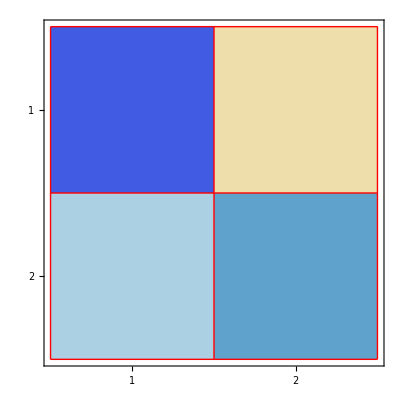

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
G=JMatNonSym[A];
GAGt=G.A.Gᵀ;
Map[MatrixForm,{G.Gᵀ,GAGt}]
MatrixPlot[Chop[GAGt],PlotLegends->Automatic]
```

To use this in a larger matrix we target a specific entry {i,j} and embed the appropriate tiny rotation in the identity matrix.

```mathematica
SetAttributes[BigJMatNonSym,HoldFirst];
BigJMatNonSym[A_,{i_,j_}]:=Module[{m=Length[A],G},
G=IdentityMatrix[m];
G⟦{i,j},{i,j}⟧=JMatNonSym[A⟦{i,j},{i,j}⟧];
G
]
```

As always test!

```mathematica
SetAttributes[JacobiStepNonSym, HoldFirst]
JacobiStepNonSym[A_]:= Module[{AbsA=Abs[LowerTriangularize[A,-2]],ij,G},
(* Find the largest non-diagonal entry *)
ij=Reverse[Position[AbsA,Max[AbsA]]⟦1⟧];
(* Compute the Jacobi/Given rotation zapping the biggest entry *)
G=BigJMatNonSym[A,ij];
(* Update A in place *)
A=G.A.Gᵀ;
(* No need to return anything! *)
]
```

As always test.

Animation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}];
A=A0;
MaxIter=223;
ListAnimate[Table[
JacobiStepNonSym[A];MatrixPlot[Chop[A],PlotLabel->i],
{i,MaxIter}],8]
```

```mathematica
MatrixForm[A0]
MatrixForm[A]
```

(-0.686361 | 0.94498 | 0.253141 | -0.958761 | -0.409283 | 0.417068 | 0.83985
0.619882 | 0.831056 | 0.0477851 | 0.999053 | 0.163265 | -0.990303 | 0.700778
0.29804 | -0.413416 | 0.591357 | -0.807766 | 0.403721 | 0.590652 | -0.098909
-0.0394445 | -0.728158 | -0.422137 | 0.937795 | 0.411594 | -0.706274 | 0.353326
0.746242 | -0.705333 | 0.979705 | 0.428487 | 0.318967 | -0.244213 | 0.094919
0.443905 | 0.285225 | -0.183931 | -0.202565 | -0.487426 | 0.432355 | 0.387248
-0.725657 | -0.917695 | 0.00836931 | -0.529171 | 0.851881 | -0.115383 | -0.930074)

(-0.686361 | 0.896142 | 0.0644286 | 0.269337 | 0.476909 | 0.417068 | 1.28138
-0.686335 | -0.936728 | -0.555114 | 0.848094 | -0.657311 | -0.17581 | -0.39203
-0.704175 | 0.0630675 | 1.16016 | -0.728364 | -0.287992 | -0.301106 | 0.422217
-0.350059 | -0.718233 | 0.00875979 | 1.03697 | 0.510911 | 1.14285 | 0.889005
-0.387095 | -0.118599 | 0.287992 | 0.522464 | -0.249832 | 0.563777 | 0.723529
0.443905 | 0.403988 | 0.451653 | 0.0150746 | 0.259663 | 0.432355 | 0.330021
0.564615 | 0.483646 | -0.124538 | -0.889005 | 0.292392 | -0.394755 | 0.738533)

Things to note, something about our choices is pushing the negative eigenvalues up and the positive eigenvalues down!  Other choices will do other things! The common choice is to push the big (either positive or negative eigenvalues up) and the small eigenvalues down!

This algorithm has more parallelism the standard “QR” Francis algorithm we are going to learn.  It has a developed very quaternionic G4 version that block diagonalizes symmetric matrices.  I am working on an alternative G4 and a G8 algorithm that make progress with a simple plan of “move the big entries up”.

It is common for

## Bisection

An m×m symmetric tridiagonal matrix 
	A=(a_1 | b_1 |   |  
b_1 | a_2 | b_2 |  
  | b_2 | a_3 | ⋱
  |   | ⋱ | ⋱)
is irreducible if b_i≠0 for any i.   If some b_i=0 we can split A into smaller non-interacting sub matrices! Look at the pattern for the eigenvalues of the top k×k submatrix A^(k)=A⟦1;;k,1;;k⟧.

```mathematica
m=5;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
A=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
TableForm[Table[
Sort[Eigenvalues[A⟦1;;k,1;;k⟧]],{k,1,m}],
TableDepth->1,TableHeadings->Automatic,TableAlignments->Center
]
```

1 | {-0.0973002}
2 | {-0.610217,0.401973}
3 | {-0.818426,-0.372624,0.456299}
4 | {-0.97473,-0.50712,0.378399,0.636144}
5 | {-1.00594,-0.54085,-0.0703224,0.4378,0.866577}

The eigenvalues interlace in the sense that λ_j^(k+1)<λ_j^(k)<λ_(j+1)^(k+1) where λ_j^k is the j^theigenvalue of the top k×k submatrix.  This property is called “interlacing”.  It is actually true for all real symmetric matrices!

Computing det(A^(k)) is cheap since det(A^(k))=a_k det(A^(k-1))-b_(k-1)^2 det(A^(k-2)).  We actually want p^(k)(x)=det(A^(k)-x Id) which is simply
	p^(k)(x)=(a_k-x)p^(k-1)(x)-b_(k-1)^2 p^(k-2)(x) with p^(-1)(x)=0 and p^(0)(x)=1.
The Sturm sequence p^(0)(x),p^(1)(x),…,p^(m)(x) can be computed cheaply.

```mathematica
Clear[p,a,b,k,x]
p[{a_,b_},-1,x_]=0;
p[{a_,b_},0,x_]=1;
p[{a_,b_},1,x_]:=p[{a,b},1,x]=(a⟦1⟧-x)
p[{a_,b_},k_,x_]:=p[{a,b},k,x]=(a⟦k⟧-x)p[{a,b},k-1,x]-b⟦k-1⟧^2 p[{a,b},k-2,x]
```

We can use this trick to count eigenvalues

```mathematica
m=5;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
A=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
Table[p[{a,b},k,0],{k,0,m}]
Eigenvalues[A]
```

{1,-0.15102,-0.686342,-0.408022,-0.0811343,0.222821}

{1.75142,-1.56974,1.00848,0.293238,-0.274063}

We can use this trick to count eigenvalues in an interval

## Divide and Conquer

### Eigen values of Diagonal Plus Symmetric Rank One

### Splitting the Problem

Divide and conquer recursively splits tridiagonal matrix into smaller tridiagonal matrices.  An example will clarify some of this

```mathematica
SetOptions[MatrixPlot, Mesh->All,PlotLegends->Automatic];
s=4;m=2 s;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
{T1,T2}={T1Hat,T2Hat}={T⟦1;;4,1;;4⟧,T⟦5;;8,5;;8⟧};
β=T⟦s+1,s⟧;T1Hat⟦-1,-1⟧-=β; T2Hat⟦1,1⟧-=β;
THat= ArrayFlatten[({{T1Hat, 0}, {0, T2Hat}})];
vec =SparseArray[{s->1,s+1->1},m];
ROne=β KroneckerProduct[vec,vec];
TabView[{
"T"->MatrixPlot[T],
"THat"->MatrixPlot[THat],
"ROne"->MatrixPlot[ROne],
"THat+ROne"->MatrixPlot[THat+ROne]}]
```

1234

Compute the eigen decomposition of the smaller matrices
	(T̂)_1=Q_1.D_1.Q_1^ᵀ  and (T̂)_1=Q_1.D_1.Q_1^ᵀ
then if z=(Q_1⟦-1⟧ | Q_2⟦1⟧) i.e the first row of Q_2 appended to the last row of Q_1then
	T=(Q_1 |  
  | Q_2).((D_1 |  
  | D_2)+β z⊗z).(Q_1^ᵀ |  
  | Q_2^ᵀ)	
This means we can focus on the inside matrix which is diagonal plus rank one

```mathematica
s=4;m=2 s;{a,b}={RandomReal[{-1,1},m],RandomReal[{-1,1},m-1]};
T=SparseArray[{Band[{1,1}]->a,Band[{1,2}]->b,Band[{2,1}]->b},{m,m}];
{T1,T2}={T1Hat,T2Hat}={T⟦1;;4,1;;4⟧,T⟦5;;8,5;;8⟧};
β=T⟦s+1,s⟧;T1Hat⟦-1,-1⟧-=β; T2Hat⟦1,1⟧-=β;
{{λ1,Q1},{λ2,Q2}}=Map[Eigensystem,{T1Hat,T2Hat}];{Q1,Q2}=Map[Transpose,{Q1,Q2}];
z=Join[Q1⟦-1⟧,Q2⟦1⟧];
BigQ=ArrayFlatten[({{Q1, 0}, {0, Q2}})];
InsideMat = SparseArray[Band[{1,1}]->Join[λ1,λ2],{m,m}]+β KroneckerProduct[z,z];
Norm[T-BigQ.InsideMat.BigQᵀ]
```

3.67676×10^-15